# Parser

Parser for the grammar:

## Recursive descent parser

```mathematica
MapUntilArg[f_,expr_,test_]:=Drop[
NestWhileList[
{f[#[[2,1]]],Drop[#[[2]],1],(!test[#[[2,1]]] && Length[#[[2]]]≠1)}&,
{0,expr,True},
#[[3]]&
][[All,1]],
1];

MapUntil[f_,expr_,test_]:=Drop[
NestWhileList[
{f[#[[2,1]]],Drop[#[[2]],1],(!test[f[#[[2,1]]]]&& Length[#[[2]]]≠1)}&,
{0,expr,True},
#[[3]]&
][[All,1]],
1];

MapWhileArg[f_,expr_ /;Length[expr]==1,test_]:=If[test[First[expr]],{f[First[expr]]},{}];
MapWhileArg[f_,expr_ /;Length[expr]>1,test_]:=Drop[
NestWhileList[
{f[#[[2,1]]],Drop[#[[2]],1]}&,
{0,expr},
(test[#[[2,1]]] && Length[#[[2]]]≠1)&
][[All,1]],
1];
```

```mathematica
MapUntil[f,Range[5],#=!=$Failed&]
```

{$Failed,2}

```mathematica
MapUntil[f,Range[5],#===7&]
```

{$Failed,2,3,4,5}

```mathematica
Protect[EmptyString,Term,NonTerm];

Match[input_,terms_]:=(Take[input,Length[terms]] == terms);
GetArgument[_[arg_]]:=arg;

MatchTerminalsWithRule[input_,rule_]:=Block[{terms,rest,matched,cuttedInput,currentState = rule["From"]},
If[rule["To"]===EmptyString,Return[{{currentState->EmptyString},{},input}]];

terms = MapWhileArg[GetArgument,rule["To"],Head[#]=!=NonTerm&];
rest = Drop[rule["To"],Length[terms]];

If[Length[terms]>Length[input],Return[$Failed]];

If[Match[input,terms],
matched = Thread[currentState->terms];
cuttedInput = Drop[input,Length[terms]];
Return[{matched,rest,cuttedInput}];
,
Return[$Failed];
];
];

MatchTerminals[NonTerm[state_],input_,grammar_]:=Block[{possibleTransitions,matched},
possibleTransitions = Cases[grammar,KeyValuePattern[{"From"->NonTerm[state]}]];
matched = Last[MapUntil[MatchTerminalsWithRule[input,#]&,possibleTransitions,#=!=$Failed&]];
Return[matched];
];

MatchTerminals[Term[state_],input_,grammar_]:=Block[{},

];
```

```mathematica
grammar = {
<|"From"->NonTerm["E"],"To"->{Term["i"],NonTerm["E'"],NonTerm["V"]}|>,
<|"From"->NonTerm["V"],"To"->{Term["j"],NonTerm["V"]}|>,
<|"From"->NonTerm["V"],"To"->EmptyString|>,
<|"From"->NonTerm["E'"],"To"->{Term["+"],Term["i"],NonTerm["E'"]}|>,
<|"From"->NonTerm["E'"],"To"->EmptyString|>
};
```

```mathematica
MatchTerminals[NonTerm["E'"],{"+","i","$"},grammar]
```

{{NonTerm[E']→+},{NonTerm[T],NonTerm[E']},{i,$}}

Parse

```mathematica
AddIdToSingleTransition[n_,m_,a_->b_]:={n,a}->{m,b};
AddIdToTransition[currentId_,transitions_]:=MapIndexed[AddIdToSingleTransition[currentId,currentId+First[#2],#1]&,transitions];
StackSymbols[caller_,id_,list_]:=Map[<|"Caller"->caller,"Id"->id,"Symbol"->#|>&,list];

Parse[input_,grammar_]:=Block[{start,inputBuffer,parseSymbol,parseTree,stack,transitions,next,currentId,newId},
start = First[grammar]["From"];
inputBuffer = Characters[StringJoin[input,"$"]];

parseSymbol = start;
parseTree = {};
stack ={};
currentId = 0;

While[{inputBuffer,parseSymbol} =!= {{"$"},None},

If[Head[parseSymbol]===NonTerm,
(* Process Non Terminal *)
{transitions,next,inputBuffer}=MatchTerminals[parseSymbol,inputBuffer,grammar];

AppendTo[parseTree,AddIdToTransition[currentId,transitions]];
newId = currentId+Length[transitions]+1;

If[Length[next] > 0,
(* If there is an available transition, take it *)
AppendTo[parseTree,{currentId,parseSymbol}->{newId,First[next]}];
{parseSymbol,stack} ={First[next],Join[stack,StackSymbols[parseSymbol,currentId,Rest[next]]]};
,
(* If not, try to restore the last state in the stack *)
If[Length[stack] > 0,
AppendTo[parseTree,{Last[stack]["Id"],Last[stack]["Caller"]}->{newId,Last[stack]["Symbol"]}];
{parseSymbol,stack} = {Last[stack]["Symbol"],Drop[stack,-1]};
,
parseSymbol = None;
]
];

currentId= newId;
,
(* Process Terminal *)

]
]
];

Return[Flatten[parseTree,1]];

];

ParseTree[input_,grammar_]:=Block[{parseTree,startProduction},
parseTree = Parse[input,grammar];
startProduction = First[First[parseTree]];

TreePlot[parseTree,Automatic,startProduction,VertexLabeling->True]
];
```

Grammar 1

```mathematica
grammar = {
<|"From"->NonTerm["E"],"To"->{Term["i"],NonTerm["E'"],NonTerm["V"]}|>,
<|"From"->NonTerm["V"],"To"->{Term["j"],NonTerm["V"]}|>,
<|"From"->NonTerm["V"],"To"->EmptyString|>,
<|"From"->NonTerm["E'"],"To"->{Term["+"],Term["i"],NonTerm["E'"]}|>,
<|"From"->NonTerm["E'"],"To"->EmptyString|>
};
```

```mathematica
Parse["i+i+ijj",grammar]
```

{{0,NonTerm[E]}→{1,i},{0,NonTerm[E]}→{2,NonTerm[E']},{2,NonTerm[E']}→{3,+},{2,NonTerm[E']}→{4,i},{2,NonTerm[E']}→{5,NonTerm[E']},{5,NonTerm[E']}→{6,+},{5,NonTerm[E']}→{7,i},{5,NonTerm[E']}→{8,NonTerm[E']},{8,NonTerm[E']}→{9,EmptyString},{1,NonTerm[E]}→{10,NonTerm[V]},{10,NonTerm[V]}→{11,j},{10,NonTerm[V]}→{12,NonTerm[V]},{12,NonTerm[V]}→{13,j},{12,NonTerm[V]}→{14,NonTerm[V]},{14,NonTerm[V]}→{15,EmptyString}}

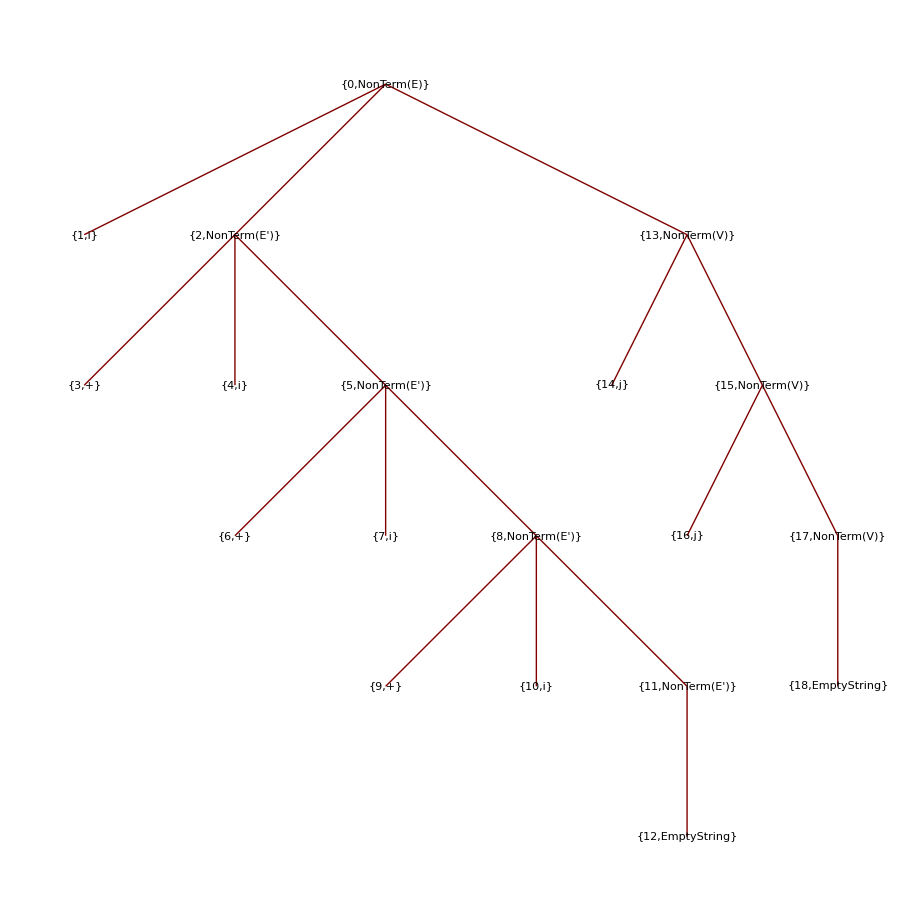

```mathematica
ParseTree["i+i+i+ijj",grammar]
```

```mathematica
.b4
```

Grammar 2

```mathematica
grammar = {
<|"From"->NonTerm["E"],"To"->{NonTerm["T"],NonTerm["E'"]}|>,
<|"From"->NonTerm["E'"],"To"->{Term["+"],NonTerm["T"],NonTerm["E'"]}|>,
<|"From"->NonTerm["E'"],"To"->EmptyString|>,

<|"From"->NonTerm["T"],"To"->{NonTerm["F"],NonTerm["T'"]}|>,
<|"From"->NonTerm["T'"],"To"->{Term["*"],NonTerm["F"],NonTerm["T'"]}|>,
<|"From"->NonTerm["T'"],"To"->EmptyString|>,

<|"From"->NonTerm["F"],"To"->{Term["i"]}|>,
<|"From"->NonTerm["F"],"To"->{Term["("],NonTerm["E"],Term[")"]}|>
};
```

```mathematica
ParseTree["(i+i)",grammar]
```

$Aborted